## [ OLD ]

Preamble

## Package Imports

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
```

Foreword, etc.

Preliminaries

## Properties of Complex Numbers

### 0.) Preamble

```mathematica
z=1/2+1/2 √3 I;
w=-1/2+1/2 √3 I;
con=3;
w^6//Expand;
```

### 1)

```mathematica
Abs[z];
Abs[w];
Abs[z w];
Abs[z w]===Abs[z]Abs[w]
```

True

### 2)

```mathematica
Abs[w];
Abs[con w];
con Abs[w];
Abs[con w]===con Abs[w]
```

True

### demo)

```mathematica
Abs[ww]"1)"//TraditionalForm
"1)   "  Abs[ww]//TraditionalForm
```

1) Abs[ww]

1)    Abs[ww]

## Triangle Inequality Theorem

```mathematica
Abs[z+w]<=Abs[z]+Abs[w]
```

True

## Reverse Triangle Inequality Theorem

```mathematica
Abs[z+w]<=Abs[z]+Abs[w]
```

True

## Stereographic Projection

(* https://mathematica.stackexchange.com/questions/23793/stereographic-projection *)

Analytic Functions

## Testing Analyticity

```mathematica
FunctionAnalytic[Sqrt[z],z,Complexes]
FunctionAnalytic[{Sqrt[z],Re[z]>0},z,Complexes]
```

False

True

```mathematica
FunctionAnalytic[z^3,z,Complexes]
```

True

```mathematica
FunctionAnalytic[Zeta[z],z,Complexes]
FunctionAnalytic[{Zeta[z],z!=1},z,Complexes]
```

False

True

## Function Visualization

## Cauchy Riemann Equations

[ TBD ]

```mathematica
f[z_]:=z^3-z^2
ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}
```

-x^2+x^3+y^2-3 x y^2+ⅈ (-2 x y+3 x^2 y-y^3)

```mathematica
Refine[Re[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}]
Refine[Im[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}]
```

-x^2+x^3+y^2-3 x y^2

-2 x y+3 x^2 y-y^3

```mathematica
D[Refine[Re[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}],x]
D[Refine[Im[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}],y]

D[Refine[Re[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}],y]
-D[Refine[Im[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}],x]
```

-2 x+3 x^2-3 y^2

-2 x+3 x^2-3 y^2

2 y-6 x y

2 y-6 x y

## Length of a path

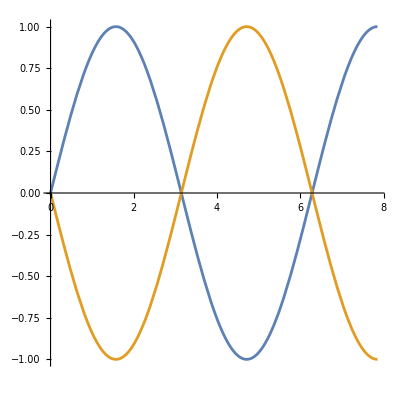

```mathematica
f[x_]:=Sin[x]
Plot[{f[x],Cos[x+Pi/2]},{x,0,2.5Pi},AspectRatio->1]
```

```mathematica
f'[t];
Integrate[√(1+f'[t]^2),{t,0,2Pi}];
Table[Integrate[√(1+Cos'[t-Pi/2]^2),{t,k/2 Pi,2Pi+k/2 Pi}],{k,0,2}]//TableForm
```

4 √2 EllipticE[1/2]
4 √2 EllipticE[1/2]
4 √2 EllipticE[1/2]

Notes

## tmp. notes

```mathematica
ContourIntegrate[z^2,z∈Line[{{0,0},{1,1}}]]
```

-2/3+(2 ⅈ)/3

```mathematica
(1+I)^3/3//Simplify
```

-2/3+(2 ⅈ)/3

```mathematica
ContourIntegrate[z^2,z∈Line[{{0,0},{0,1},{1,0},{1,1}}]]
```

-2/3+(2 ⅈ)/3

```mathematica
CoordinateTransform["Polar"->"Cartesian",{r,θ}]
CoordinateTransform["Cartesian"-> "Polar",{x,y}]
CoordinateTransform["Cartesian"-> "Spherical",{x,y,0}]
```

{r Cos[θ],r Sin[θ]}

{√(x^2+y^2),ArcTan[x,y]}

{√(x^2+y^2),ArcTan[0,√(x^2+y^2)],ArcTan[x,y]}

```mathematica
Conjugate[2+3I]
```

2-3 ⅈ

```mathematica
z=1+2I;
w=-1+√I;
Abs[z]Abs[w]//Simplify
Abs[z w]//Simplify
√3 Abs[z]
Abs[√3 z]
z/Abs[z]//Abs
w/Abs[w]//Abs
```

√(10-5 √2)

√(10-5 √2)

√15

√15

1

1

```mathematica
z/Abs[z]
Abs[z/Abs[z]]
```

(1+2 ⅈ)/(√5)

1

```mathematica
z Conjugate[z]
```

5

```mathematica
Abs[z]
Abs[Conjugate[z]]
```

1

1

```mathematica
ClearAll[w,z]
```

```mathematica
z
```

z

```mathematica
w
```

w

```mathematica
Import["http://www.mathematicaguidebooks.org/V6/downloads/RiemannSurfacePlot3D.m",{"Text","Lines"}];
```

```mathematica
Import["http://www.mathematicaguidebooks.org/V6/downloads/RiemannSurfacePlot3D.m"]
```

```mathematica
rsurf[func_]:=Grid[{{RiemannSurfacePlot3D[w==func,Re[w],{z,w},ImageSize->400,Coloring->Hue[Rescale[ArcTan[1.4 Im[w]],{-Pi/2,Pi/2}]],PlotPoints->{40,40},Boxed->False],RiemannSurfacePlot3D[w==func,Im[w],{z,w},ImageSize->400,Coloring->Hue[Rescale[ArcTan[1.4 Re[w]],{-Pi/2,Pi/2}]],PlotPoints->{40,40},Boxed->False]}}];
```

```mathematica
rsurf[Log[z]]
```

-Graphics3D- | -Graphics3D-

```mathematica
42/5.
```

8.4

```mathematica
ComplexAnalysis`BranchPoints[√(z^2-1),z]
ComplexAnalysis`BranchCuts[√(z^2-1),z]
```

{-1,1,ComplexInfinity}

(-1<Re[z]<0&&Im[z]==0)||Re[z]==0||(0<Re[z]<1&&Im[z]==0)

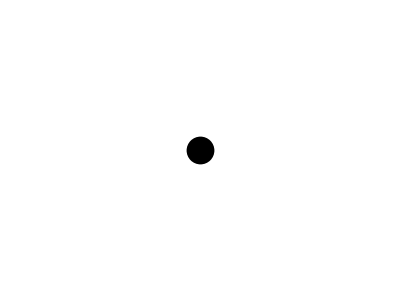
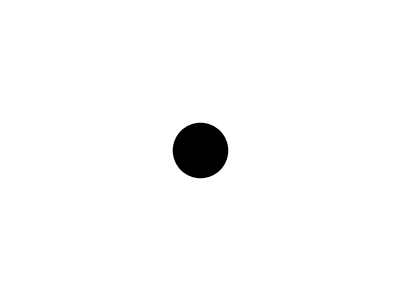
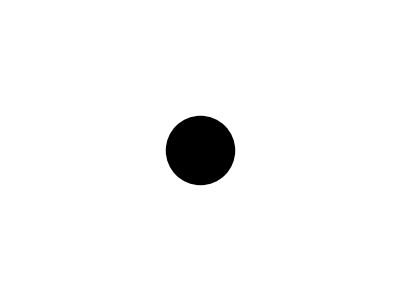
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-}

```mathematica
Table[Graphics[{PointSize[r],Point[{0,0}]}],{r,{0.02,0.05,0.1,0.3,0.5}}]
Table[Graphics[{AbsolutePointSize[r],Point[{0,0}]}],{r,{4}}]
```

## COMPLEX ANALYSIS (1)

## Ch.

### Par.

#### TOPIC

### Par.

#### TOPIC

```mathematica
2Exp[2/3 Pi I]//ExpToTrig
2Exp[4/3 Pi I]//ExpToTrig
```

-1+ⅈ √3

-1-ⅈ √3

```mathematica
(-1+I √3)^3//Expand
(-1-I √3)^3//Expand
```

8

8

## Visualizing Functions

### Par.

#### TOPIC

### Par.

#### TOPIC

## UZT’s Mathematica